```mathematica
(*Table 1*)
```

```mathematica
alphaB[r_]:=((r-1)^2/(2r))^(1/(2r))(1/2(2r-1)!!)^(1/(2r^2))((2r^2)/(2r-1))^(1/(2r-2))(2r-1)/(2r-2);alpha[r_]:=((r-1)/4)^(1/(2r))(1/2(2r-1)!!)^(1/(2r^2))((2r^2)/(2r-1))^(1/(2r-2))(2r-1)/(2r-2);betaB[r_]:=2r/(r-1)(3005/1000+Log[4((2r-1)/(2r^2))^(r/(r-1))/(1/2(2r-1)!!)^(1/r)]);beta[r_]:=2r/(r-1)(-9983/10000+Log[4((2r-1)/(2r^2))^(r/(r-1))/(1/2(2r-1)!!)^(1/r)]);Table[{r,N[alpha[r],8],N[alphaB[r],8],N[beta[r],8],N[betaB[r],8]},{r,2,15}]//MatrixForm
```

(2 | 1.8220993 | 1.8220993 | -7.1055868 | 8.9076132
3 | 1.7156492 | 1.7999134 | -6.6151222 | 5.3947778
4 | 1.6409414 | 1.7262532 | -7.0097154 | 3.6657513
5 | 1.5766362 | 1.6525077 | -7.4677781 | 2.5404719
6 | 1.5228978 | 1.5891253 | -7.9020468 | 1.7058732
7 | 1.4781891 | 1.5362087 | -8.3005788 | 1.0404545
8 | 1.4407284 | 1.4920109 | -8.6648803 | 0.48551968
9 | 1.409006 | 1.454772 | -8.9989561 | 0.0084688855
10 | 1.3818424 | 1.4230565 | -9.3068546 | -0.41063235
11 | 1.3583356 | 1.3957537 | -9.5921189 | -0.78485887
12 | 1.3377959 | 1.3720131 | -9.8577273 | -1.1232546
13 | 1.3196921 | 1.3511815 | -10.106158 | -1.432341
14 | 1.3036101 | 1.332752 | -10.339472 | -1.71698
15 | 1.289224 | 1.3163275 | -10.559397 | -1.9808966)

```mathematica
(*Proof of Lemma 4*)
```

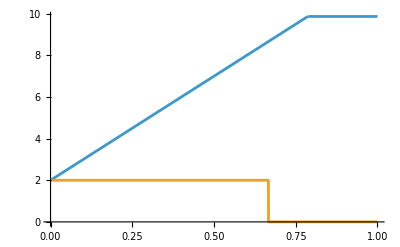
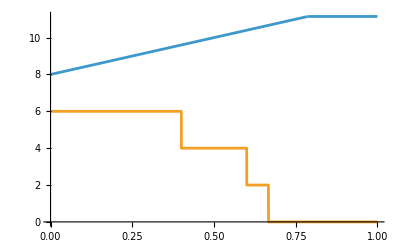
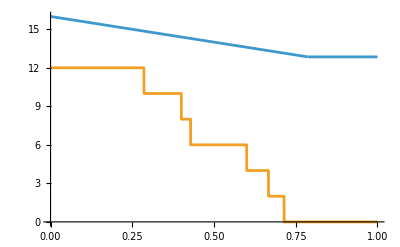

```mathematica
Table[cp[c_]:=Max[1-c,13/61];Plot[{12+cp[c](piA^2+piA-16),2Sum[i-PrimePi[c Prime[i]]-1,{i,2,piA}]},{c,0,1}],{piA,2,4}]
```

```mathematica
(*Proof of Theorem 6*)
```

```mathematica
(*Equation (8)*)
```

```mathematica
p=10^3;Table[B0=(1/2(2r-1)!!)^(1/r)p^(1/(2r));lhs=B0^2(1-Exp[(-r(2r-1)/(B0+1))]);rhs=(1/2(2r-1)!!)^(2/r)p^(1/r-1/2)/(2-1/Sqrt[p])+r(r-1)/(2-1/Sqrt[p]);lhs>=rhs,{r,2,15}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(*Verification of Hypothesis 2*)
```

```mathematica
Table[2^(-r/(r-1))/(1/2(2r-1)!!)^(1/r)<1,{r,2,15}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(*Proof of Theorem 2*)
```

```mathematica
(*Verification of Hypothesis 7*)
```

```mathematica
nextOdd[n_]:=Ceiling[(n-1)/2]*2+1
```

```mathematica
Table[(1/2(2r-1)!!)^(1/r)(10^23)^(1/(2r))>=2r,{r,2,15}]//N
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(*Upper bound on W/(2B+1)^(2r-1)*)
```

```mathematica
p=10^23;Table[B0=(1/2(2r-1)!!)^(1/r)p^(1/(2r));lhs=B0^2(1-Exp[(-r(2r-1)/(B0+2))]);rhs=4r(r-1)/(2-2/Sqrt[p])+(1/2(2r-1)!!)^(2/r)p^(1/r-1/2)/(2-1/Sqrt[p]);lhs>=rhs,{r,2,15}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(*Upper bound on A/N_0*)
```

```mathematica
p=10^23;Table[2((2r-1)/(2r^2))^(r/(r-1))/nextOdd[(1/2(2r-1)!!)^(1/r)p^(1/(2r))]//N,{r,2,15}]//Max
```

0.00167361

```mathematica
(*Checking it is enough to have K>=\alpha(r)D(p,r,c_0')^{1/2r}, for A >= 10^5 *)
```

```mathematica
gammaMaxTable={Null,1.23228,1.31890,1.35539,1.37540,1.38804,1.39674,1.40309,1.40793,1.41174,1.41482,1.41735,1.41948,1.42130,1.42286};
aMin=10^5;
Table[gammaMax=gammaMaxTable[[r]];
e=2r*5.14/(r-1);dMin=Floor[Log[10^23]+beta[r]+4r/(r-1)*13/61,10^-2];(e-r/(2r-1)*dMin)+(e*-r/(2r-1)+dMin*gammaMax)/Log[aMin]+(e*gammaMax)/Log[aMin]^2<0,{r,2,15}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(*Checking it is enough to have K>=\alpha(r)D(p,r,c_0')^{1/2r}, for A < 10^5. Took about 10 seconds on my laptop *)
```

```mathematica
Table[dMin=Floor[Log[10^23]+beta[r]+4r/(r-1)*13/61,10^-2];Ar=2((2r-1)/(2r^2))^(r/(r-1))(10^23)^((r+1)/(4r))/((1/2(2r-1)!!)^(1/r)(10^23)^(1/(2r))+2);firstk=PrimePi[Ar]-1;fsum=Sum[N[i/Prime[i],20],{i,5,firstk}];gsum=Sum[N[Prime[i]^(1-1/r),20],{i,1,firstk}];(Table[fsum+=N[k/Prime[k],20];gsum+=N[Prime[k]^(1-1/r),20];fPart=(2r)/(r-1)*Prime[k+1]/k(1+2(122/105+fsum)/k+0.0017(k^2+k-4)/(k Prime[k]));gPart=((2r-2)/(2r-1-(2-1/r)gsum/(k Prime[k]^(1-1/r))))^(2r);fPart*gPart,{k,firstk+1,9592}]//Max)<dMin,{r,2,15}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(*Verification of Hypothesis 6*)
```

```mathematica
Table[4((2r-1)/(2r^2))^(r/(r-1))/(1/2(2r-1)!!)^(1/r)<1,{r,2,15}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(*Proof of Lemma 5*)
```

```mathematica
(*r_1; note here we have divided through by A first*)
```

```mathematica
Table[pkp1=Prime[k+1];1/k^2<=Min[5/(4pkp1),Log[pkp1]^2/pkp1^2+20/pkp1^3],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
(*r_2*)
```

```mathematica
Table[pkp1=Prime[k+1];1/k^2<=Min[1/4,Log[pkp1]^2/pkp1^2+3.7/pkp1^2],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
(*r_3*)
```

```mathematica
Table[pkp1=Prime[k+1];1/k<=Min[1/2,Log[pkp1]/pkp1+4.5/pkp1^2],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
(*r_4; each value in the first slot corresponds to the value in the second slot of the line above*)
```

```mathematica
list=Table[{Prime[k+1],N[Prime[k+1]/k-Log[Prime[k+1]]+1,20]},{k,2,1415}]//Reverse;max=-10;Do[If[i[[2]]>max,Print[i];max=i[[2]]],{i,list}]
```

{11813,-0.028546004955587068547}

{11807,-0.026377133549259667514}

{11801,-0.024205653121148566189}

{11783,-0.023598068908237948384}

{11779,-0.020172854738926337186}

{11777,-0.015493535827354012801}

{7487,-0.014904454838921749557}

{7481,-0.012087925233927114444}

{7477,-0.0074176088306033734538}

{7451,-0.006337076201285890883}

{5413,-0.004693389153219127732}

{5407,-0.001348565786499232604}

{5399,-0.00043879111842762736263}

{5393,0.0029175525500969293836}

{5387,0.0062814651897060196081}

{5381,0.0096529763862865698135}

{3527,0.015096458765984665794}

{3511,0.016302924036066734698}

{3461,0.016318626343951813699}

{3457,0.024042730202856793788}

{3449,0.024638557541329571385}

{3301,0.027608900976180637089}

{3299,0.039317969464059269443}

{2657,0.052383868861596416917}

{1973,0.055787137075027751527}

{1451,0.056236288600528310655}

{1447,0.069243501438691577324}

{1433,0.073182536773598061428}

{1429,0.086380933181243704659}

{1427,0.10720609680887786881}

{1423,0.12064332119265884162}

{809,0.1243449678335946415}

{599,0.15103469818084694749}

{593,0.15686167576862968764}

{587,0.16271102922850732528}

{569,0.18039141053386325378}

{563,0.18632821499756451996}

{557,0.19228624522123082957}

{419,0.19962908007786226897}

{349,0.20289909229032645999}

{347,0.25361639652372904294}

{227,0.30421664918526399165}

{223,0.3375090796037110286}

{149,0.37840663523101144724}

{127,0.38914624687474206029}

{101,0.42487948315874054912}

{97,0.46695568816328384455}

{71,0.47416222822184247341}

{67,0.51752960283125616255}

{59,0.60996255609428054938}

{41,0.7030945999623588628}

{37,0.752718450992139192}

{29,0.85492639223574819504}

{17,1.0001199892771172531}

{13,1.0350506425384632639}

{11,1.3521047272016294559}

{7,1.3874231842780200282}

{5,1.8905620875658996254}

```mathematica
(*r_5*)
```

```mathematica
total=0;Do[total+=N[i/Prime[i],20];If[-1+Prime[i+1]/i^2*total<255/100/Log[Prime[i+1]],,Print["False at ",i]],{i,1,PrimePi[10^5]}]
```

```mathematica
(*Proof of Lemma 9*)
```

```mathematica
N[{6a/Log[a]^4,LogIntegral[a]-a/Log[a]-a/Log[a]^2-2a/Log[a]^3,(21/2)a/Log[a]^4}/.a->10^5,6]
```

{34.1514,58.4117,59.7649}

```mathematica
(*Proof of Lemma 15*)
```

```mathematica
list=Table[i/Prime[i],{i,1,39016}];N[Min[list],10]
```

0.08346186181

```mathematica
i=39017;u=Exp[-0.0516];lastk=Floor[u i];min=Table[j/Prime[j],{j,1,lastk}]//Min;test=i/Prime[i];Print[test≤min," at i = ",i];Do[newk=Floor[u i];test=i/Prime[i];If[newk>lastk,min=Min[min,newk/Prime[newk]]];If[test≤min,,Print["False at ",i]],{i,39018,40901}]
```

True at i = 39017

```mathematica
(*Proof of Lemma 16; took about 10 seconds on my laptop*)
```

```mathematica
u=Exp[-0.0516];N[Table[Prime[Floor[u i]]/Prime[i],{i,33,39016}]//Min,8]
```

0.87665198

```mathematica
(*Proof of Theorem 17; took a few minutes on my laptop. Could be made significantly more efficient*)
```

```mathematica
list=Table[i/Prime[i],{i,1,39016}];incnList={{48/61,5},{103/121,62},{224/263,122}}
```

{{48/61,5},{103/121,62},{224/263,122}}

```mathematica
Do[in=incnList[[n,2]];cn=incnList[[n,1]];Do[pk=NextPrime[cn Prime[i]];k=PrimePi[pk];min=Min[list[[1;;k]]];If[min≥list[[i]],,Print[{n,i}]],{i,in,39016}],{n,1,3}]
```

{1,6}

{1,8}

{1,11}

{1,14}

{1,61}

{2,121}

{2,263}

{3,263}

```mathematica
exceptionsList={{1,{6,8,11,14,61}},{2,{121,263}},{3,{263}}};Table[exceptions=exceptionsList[[n,2]];c=incnList[[n,1]];Table[k=PrimePi[c*Prime[i]];{n,(list[[1;;k]]//Min)≥list[[i]],i,k,i-k-1,(1-c)i},{i,exceptions}],{n,1,3}]//Catenate//MatrixForm
```

(1 | True | 6 | 4 | 1 | 78/61
1 | True | 8 | 6 | 1 | 104/61
1 | True | 11 | 9 | 1 | 143/61
1 | True | 14 | 11 | 2 | 182/61
1 | True | 61 | 47 | 13 | 13
2 | True | 121 | 102 | 18 | 18
2 | True | 263 | 223 | 39 | 4734/121
3 | True | 263 | 223 | 39 | 39)

```mathematica
(*Proof of Lemma 19*)
```

```mathematica
f[x_]:=(ExpIntegralEi[x]-Exp[x]/x-Exp[x]/x^2)*(x^3/Exp[x]);N[f[1726/100],6]
```

2.46669

```mathematica
g[x_]:=f[x]-2x/(x-3);N[g[1726/100],6]
```

0.0459285

```mathematica
h[x_]:=ExpIntegralEi[x]-Exp[x]/x-Exp[x]/x^2-2Exp[x]/x^3;N[h[1726/100],6]
```

2843.32

```mathematica
(*Proofs of Lemmas 20 and 22*)
```

```mathematica
Do[Print[r];K1=-ExpIntegralEi[(2-1/r)Log[11813]];K2=-(2-1/r)ExpIntegralEi[(2-1/r)Log[11813]]+11813^(2-1/r)/Log[11813];K3=-1/2((2-1/r)^2ExpIntegralEi[(2-1/r)Log[11813]]-11813^(2-1/r)(1+(2-1/r)Log[11813])/Log[11813]^2);c1=Interval[{2,247/100}];c2=Interval[{2,247/100}];c3=Interval[{2,247/100}];c4=Interval[{146184/100000,253816/100000}];K4=r/(r-1)(1416Prime[1416]^(1-1/r)-Sum[Prime[i]^(1-1/r),{i,1,1416}]);K5=K1+K2+K4+c4 K3;c5=c1/(2-1/r)^2+c2/(2-1/r)+c3 c4/2;c6=Interval[{-153816/100000,-30273/100000}];minA=10^5;gamma1=-(1-1/r)(c5+c6-(3-1/r)/(2-1/r)+(c6(3-1/r)/(2-1/r)-c5)Interval[{0,1/Log[minA]}]+c5 c6 Interval[{0,1/Log[minA]^2}]+K5(2-1/r)Interval[{0,Log[minA]^3/minA^(2-1/r)}]-K5(2-1/r)Interval[{0,Log[minA]^2/minA^(2-1/r)}]+c6 K5(2-1/r)Interval[{0,Log[minA]/minA^(2-1/r)}]);Print[N[gamma1,10]];eps=(r-1)/(2r-1)Interval[{0,1/Log[minA]}]-gamma1 Interval[{0,1/Log[minA]^2}];u=Interval[eps[[1,2]]];
gamma2Lower=(Exp[-r/(r-1)u]+r/(r-1)u-1)/u^2;gamma2Upper=((1-u)^(-r/(r-1))-r/(r-1)u-1)/u^2;gamma2=Interval[{gamma2Lower[[1,1]],gamma2Upper[[1,2]]}];gamma3=gamma1*r/(r-1)+gamma2*((r-1)/(2r-1))^2-2gamma1*gamma2*(r-1)/(2r-1)Interval[{0,1/Log[minA]}]+gamma2 gamma1^2Interval[{0,1/Log[minA]^2}];Print[N[gamma3,10]],{r,2,15}]
```

2

Interval[{-1.96258345,0.2119139289}]

Interval[{-3.748373306,1.232266826}]

3

Interval[{-2.411770003,0.384432488}]

Interval[{-3.4957026,1.318893747}]

4

Interval[{-2.618747775,0.480543137}]

Interval[{-3.39186355,1.355375996}]

5

Interval[{-2.738621704,0.5406780605}]

Interval[{-3.335422835,1.375394795}]

6

Interval[{-2.816977152,0.5816717675}]

Interval[{-3.299984319,1.388029335}]

7

Interval[{-2.872245632,0.6113611607}]

Interval[{-3.275671442,1.396725672}]

8

Interval[{-2.91333694,0.6338392853}]

Interval[{-3.257958335,1.403075684}]

9

Interval[{-2.945092789,0.6514423296}]

Interval[{-3.244479898,1.407915611}]

10

Interval[{-2.970373228,0.6655980634}]

Interval[{-3.233880174,1.411726665}]

11

Interval[{-2.990977268,0.6772272999}]

Interval[{-3.225326139,1.414805296}]

12

Interval[{-3.008093524,0.6869501816}]

Interval[{-3.21827783,1.417344076}]

13

Interval[{-3.022539008,0.6951994773}]

Interval[{-3.212369915,1.419473525}]

14

Interval[{-3.034893906,0.7022863034}]

Interval[{-3.207346384,1.421285234}]

15

Interval[{-3.045581625,0.7084400245}]

Interval[{-3.203022513,1.422845369}]

```mathematica
(*Proof of Lemma 23*)
```

```mathematica
N[Sum[i/Prime[i],{i,1,PrimePi[10^5]}],8]
```

1051.4282

```mathematica
PrimePi[10^5](1/Log[10^5]+1.2762/Log[10^5]^2)
```

925.505